```mathematica
(* Question 1 *)
j=I;
PI[x_]:=Piecewise[{
{1,Abs[x]≤ 1/2},
{0,Abs[x]>1/2}
}]
(*F=FourierTransform[-E^(-5 t)UnitStep[t-1],t,ω,FourierParameters->{1,-1}];*)
F=F//FullSimplify//TrigToExp;
F=Integrate[4 E^(-j ω t),{t,0,1}]+Integrate[2 E^(-j ω t),{t,1,2}]//FullSimplify//TrigToExp
FullSimplify[F==  (4j E^(-j (3 ω)/2))/ω Cos[ω/2]-(4j)/ω]
```

-(4 ⅈ)/ω+(2 ⅈ ⅇ^(-ⅈ ω))/ω+(2 ⅈ ⅇ^(-2 ⅈ ω))/ω

True

True

(1+ⅇ^(-2 ⅈ f π^2))/(1-4 f^2 π^2)

1/(1-4 f^2 π^2)-1/4 ⅈ (2 π DiracDelta[-1+2 f π]-2 π DiracDelta[1+2 f π])+ⅇ^(2 ⅈ f π^2) (1/(1-4 f^2 π^2)-1/4 ⅈ (2 π DiracDelta[-1+2 f π]-2 π DiracDelta[1+2 f π]))

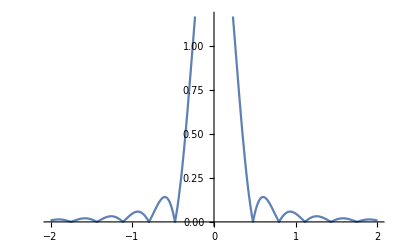

-Graphics-

```mathematica
(* Question 2 *)
j=I;
PI[x_]:=Piecewise[{
{1,Abs[x]≤ 1/2},
{0,Abs[x]>1/2}
}]
F=FourierTransform[PI[t+1/2]-PI[t-1/2],t,ω,FourierParameters->{1,-1}];
FullSimplify[F==  2j Sinc[ω/2]Sin[ω/2]]
F=FourierTransform[Sin[t](UnitStep[t]-UnitStep[t-Pi]),t,ω,FourierParameters->{1,-1}]/.{ω-> 2 Pi f}//FullSimplify
A=1/(4j)(DiracDelta[f-1/(2 Pi)]-DiracDelta[f+1/(2 Pi)])+1/(1-(2Pi f)^2)+(1/(4j)(DiracDelta[f-1/(2 Pi)]-DiracDelta[f+1/(2 Pi)])+1/(1-(2Pi f)^2))E^(j 2 Pi^2 f)//FullSimplify
Plot[Abs[F],{f,-2,2}]
Plot[Abs[A],{f,-2,2}]
```

```mathematica
(* Question 3 *)
j=I;
PI[x_]:=Piecewise[{
{1,Abs[x]≤ 1/2},
{0,Abs[x]>1/2}
}]
F=FourierTransform[PI[t+1/2]-PI[t-1/2],t,ω,FourierParameters->{1,-1}];
```